```mathematica
data=Import["C:/Users/Ian/Desktop/gravlensingproject/data.csv"];
theta=data⟦;;,1⟧;
ellipticity=data⟦;;,2⟧;
σellipticity=data⟦;;,3⟧;
```

## NFW Fit

```mathematica
H0=69.32 Quantity[, ("Kilometers")/("Megaparsecs" "Seconds")];
ρcrit=UnitConvert[(3 H0^2)/(8π Quantity[, "GravitationalConstant"]),"SI"];
DL=1 Quantity[, "Gigaparsecs"];
DS=3 Quantity[, "Gigaparsecs"];
θs=UnitConvert[M200^(1/3)/(c DL)((3 Quantity[, "SolarMass"])/(800π ρcrit))^(1/3)]*QuantityMagnitude[Quantity[, "Radians"],Quantity[, "ArcSeconds"]];
rs=UnitConvert[M200^(1/3)/c((3 Quantity[, "SolarMass"])/(800π ρcrit))^(1/3),"SI"];
δc=200/3*c^3/(Log[1+c]-c/(1+c));
```

```mathematica
surfaceDensity=(2δc*ρcrit*rs)/((θ/θs)^2-1)(1-2/(√((θ/θs)^2-1))ArcTan[√((θ/θs-1)/(θ/θs+1))]) ;
averageSurfaceDensity=(4δc*ρcrit*rs)/(θ/θs)^2(2/(√((θ/θs)^2-1))ArcTan[√((θ/θs-1)/(θ/θs+1))]+Log[(θ/θs)/2]) ;
criticalSurfaceDensity=UnitConvert[Quantity[, "SpeedOfLight"]^2/(4π Quantity[, "GravitationalConstant"])*DS/((DS-DL)*DL),"SI"];
convergence=surfaceDensity/criticalSurfaceDensity;
shear=Simplify[Expand[(averageSurfaceDensity-surfaceDensity)/criticalSurfaceDensity]];
reducedShear=shear/(1-convergence);
ellipticityNFW=(2*reducedShear)/(1+reducedShear^2);
```

```mathematica
chiSquared=Total[((ellipticity-(ellipticityNFW/.θ->theta))/σellipticity)^2];
```

```mathematica
chiSquared/.{M200->10^15,c->10}
```

0.1964

```mathematica
NMinimize[{chiSquared,10^10<M200<10^17,0<c<100},{M200,c}]
```

{0.184964,{M200→1.06626×10^15,c→9.42202}}

## Isothermal Fit

```mathematica
r200=UnitConvert[M200^(1/3)((3 Quantity[, "SolarMass"])/(800π ρcrit))^(1/3),"SI"];
σ2=(M200 Quantity[, "SolarMass"]Quantity[, "GravitationalConstant"] /Quantity[, "Meters"])/Expand[2(r200-DL θc ArcTan[r200/(DL θc)])*1/Quantity[, "Meters"]];
```

```mathematica
surfaceDensity=σ2/(2 Quantity[, "GravitationalConstant"]DL √(θ^2+θc^2)) ;
averageSurfaceDensity=(σ2(√(θ^2+θc^2)-θc))/(2 Quantity[, "GravitationalConstant"]DL θ^2) ;
criticalSurfaceDensity=UnitConvert[Quantity[, "SpeedOfLight"]^2/(4π Quantity[, "GravitationalConstant"])*DS/((DS-DL)*DL),"SI"];
convergence=surfaceDensity/criticalSurfaceDensity;
shear=Simplify[Expand[(averageSurfaceDensity-surfaceDensity)/criticalSurfaceDensity]];
reducedShear=shear/(1-convergence);
ellipticityIsothermal=(2*reducedShear)/(1+reducedShear^2)/.{θ->t*QuantityMagnitude[Quantity[, "ArcSeconds"],Quantity[, "Radians"]],θc->tc*QuantityMagnitude[Quantity[, "ArcSeconds"],Quantity[, "Radians"]]};
```

```mathematica
chiSquared=Total[((ellipticity+(ellipticityIsothermal/.t->theta))/σellipticity)^2];
```

```mathematica
NMinimize[{chiSquared,10^15<M200<10^17,0<tc<1000},{M200,tc}]
```

{0.375878,{M200→6.7446×10^15,tc→104.94}}

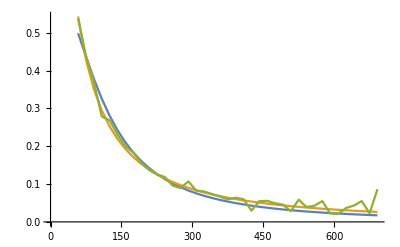

```mathematica
ListLinePlot[{
Transpose[{theta,(-ellipticityIsothermal/.{t->theta,M200->6.744595753180768*^15,tc->104.94045116064925})}],
Transpose[{theta,ellipticityNFW/.{θ->theta,M200->10^15,c->10}}],
Transpose[{theta,ellipticity}]
}]
```